# 70% Network Congestion

## How long as TWC been aware of network congestion in High Speed Internet service to Hana, HI? by A. Chase Turner For discussion purposes only. Confidential. Use or citation of this report requires specific permission of the author.

#### Utilities

```mathematica
Clear[unixTimeToHST];unixTimeToHST[x_Integer]:=DateList[AbsoluteTime[{1970,1,1,2,0,0}]+x,TimeZone->-10];
(* TEST *)
unixTimeToHST[1330434000]
```

{2012,2,28,10,0,0.}

## BuiltIn measurements for 1st and 2nd hop

#### Sources

```mathematica
(* urlForPingJSONData - answer with the JSON URL for fetching data *)
Clear[urlForPingJSONData];urlForPingJSONData::usage = "URL to get atlas.ripe.net ping data";urlForPingJSONData::unexpectedArg="`1`";
(* IMPLEMENTATION *)urlForPingJSONData[probeID_Integer,
resolution_String /;StringMatchQ[resolution, "1h" | "1d"],
hopNumber_Integer /; MatchQ[hopNumber , 1|2] , 
startDate_String, 
endDate_String]:="https://stat.ripe.net/data/atlas-ping-measurements/data.json?probe_id="<>ToString[probeID]<>"&measurement_id="<> ToString[hopNumber]<>"&starttime="<>startDate<>"&endtime="<>endDate<>"&resolution="<>resolution;
(* UNEXPECTED ARGUMENT *)
urlForPingJSONData[probeID_,resolution_,hopNumber_, startDate_, endDate_]:= Message[urlForPingJSONData::unexpectedArg,{probeID, resolution, hopNumber, startDate,endDate}];
(* TEST *)
urlForPingJSONData[1178,"1h",1,"2012-02-24T08:19:23","2014-05-09T16:50:21"]
```

https://stat.ripe.net/data/atlas-ping-measurements/data.json?probe_id=1178&measurement_id=1&starttime=2012-02-24T08:19:23&endtime=2014-05-09T16:50:21&resolution=1h

```mathematica
(* fileForPingJSONData - answer with the JSON URL for fetching data *)
Clear[fileForPingJSONData];fileForPingJSONData::usage = "URL to get atlas.ripe.net ping data";fileForPingJSONData::unexpectedArg="`1`";
(* IMPLEMENTATION *)fileForPingJSONData[probeID_Integer,
resolution_String /;StringMatchQ[resolution, "1h" | "1d"],
hopNumber_Integer /; MatchQ[hopNumber , 1|2] , 
startDate_String, 
endDate_String]:=FileNameJoin[{NotebookDirectory[],"data","atlas.ripe.net-builtIn-p"<>ToString[probeID]<>"-resolution_"<>resolution<>"-hop_"<> ToString[hopNumber]<>".json"}];
(* UNEXPECTED ARGUMENT *)
fileForPingJSONData[probeID_,resolution_,hopNumber_, startDate_, endDate_]:= Message[fileForPingJSONData::unexpectedArg,{probeID, resolution, hopNumber, startDate,endDate}];
(* TEST *)
fileForPingJSONData[1178,"1h",1,"2012-02-24T08:19:23","2014-05-09T16:50:21"]
```

/Users/chase/src/git/atlas.ripe.net/builtInMetrics/data/atlas.ripe.net-builtIn-p1178-resolution_1h-hop_1.json

```mathematica
pullAndCache[probeID_Integer,resolution_String,hopNumber_Integer]:= Block[{urlHopData, cachingFile, hardCodedStart, hardCodedEnd},
hardCodedStart="2012-02-24T08:19:23";
hardCodedEnd="2014-05-09T16:50:21";
urlHopData=Import[urlForPingJSONData[probeID,resolution,hopNumber,hardCodedStart,hardCodedEnd],"JSON"];
cachingFile=fileForPingJSONData[probeID,resolution,hopNumber,hardCodedStart,hardCodedEnd];
Export[cachingFile,urlHopData,"JSON"];
urlHopData];
```

#### JSON data file

```mathematica
(* jsonData returns data portion of the data set from the local cached file, or a new data set is pulled from atlas.ripe.net, cached, and referenced *)

Clear[jsonData];
jsonData::usage="fetch cached json data or pull from atlas";
jsonData::unexpectedArg="`1`";
jsonData::datasetMismatch ="Args `1` do not match data property in file `2`";
(* IMPLEMENTATION *)
jsonData[probeID_Integer,resolution_String,hopNumber_Integer]:=Block[{startDate="2012-02-24T08:19:23", endDate="2014-05-09T16:50:21",jsonFile, url,jsonImport,jsonData},
jsonFile=fileForPingJSONData[probeID,resolution,hopNumber,startDate,endDate];
url=urlForPingJSONData[probeID,resolution,hopNumber,startDate,endDate];
(* TODO check local; if nothing, pull from atlas and store. With result, verify  *)
jsonImport=If[FileExistsQ[jsonFile],Import[jsonFile,"JSON"],pullAndCache[probeID, resolution, hopNumber]];
(* Walk JSON data structure, asserting with each traversal it is not null *)
Block[{jsonDataProbeID, jsonDataMeasurementID,jsonDataResolution},
jsonData="data"/. jsonImport;
Assert[jsonData!={}];
(* Assert - file matches the requested probe data *)
jsonDataProbeID= "probe_id"/.jsonData;
jsonDataMeasurementID="measurement_id" /. jsonData;
jsonDataResolution ="resolution"/. jsonData;
Assert[ToString[probeID]==jsonDataProbeID];
Assert[ToString[hopNumber]==jsonDataMeasurementID];
Assert[resolution==jsonDataResolution];
];
(* CONFIRM data set referened matches argements  *)
(* ---> returning *)
jsonData
];
(* UNEXPECTED ARGUMENT *)
jsonData[probeID_, resolution_]:=Message[jsonData::unexpectedArg, {probeID, resolution}];
(* TEST *)
```

#### jsonDataMeasurementsToCDF

```mathematica
(* jsonDataMeasurementsToCDF returns CDF version of measurementData *)

Clear[jsonDataMeasurementsToCDF];
jsonDataMeasurementsToCDF::usage="convert JSON data to CDF";
jsonDataMeasurementsToCDF::unexpectedArg="`1`";
(* IMPLEMENTATION *)
jsonDataMeasurementsToCDF[probeID_Integer,resolution_String,hopNumber_Integer]:=Block[{measurements, converted},
(* Traverse JSON graph to get to measurements *)
measurements="measurements"/. jsonData[probeID,resolution,hopNumber];
(* flatten and convert values where necessary *)
(* ASSERT : format is rules as the following example
{"received"-> 6, 
"rtt_5pct"->10.088,
"rtt_95pct"->21.066,
"rtt_med"->14.8675,
"sent"->6,
"timestamp"->1330434000}
 *)
(* ---> returning *)
Join[{"probe_id"->probeID,"measurement_id"->hopNumber,"resolution"->resolution},#[[1;;5]],{"timestamp"->unixTimeToHST["timestamp"/.#[[6]]]}]& /@measurements
]
(* UNEXPECTED ARGUMENT *)
jsonDataMeasurementsToCDF[probeID_, resolution_]:=Message[jsonDataMeasurementsToCDF::unexpectedArg, {probeID, resolution}];
(* TEST *)
Dimensions[jsonDataMeasurementsToCDF[1178,"1h",1]]
```

{18600,9}

#### Combine Measurements to tMeasurements

```mathematica
tMeasurements=Join[

jsonDataMeasurementsToCDF[1165,"1h",1],
jsonDataMeasurementsToCDF[1178,"1h",1],
jsonDataMeasurementsToCDF[2289,"1h",1],
jsonDataMeasurementsToCDF[10546,"1h",1],
jsonDataMeasurementsToCDF[1165,"1h",2],
jsonDataMeasurementsToCDF[1178,"1h",2],
jsonDataMeasurementsToCDF[2289,"1h",2],
jsonDataMeasurementsToCDF[10546,"1h",2]

];
Dimensions[tMeasurements]
```

{117959,9}

```mathematica
exportToCSV[dataSet_List]:=Block[{header,distilledData},
header={"timestamp","probe_id","measurement_id","resolution","rtt_med","rtt_5pct","rtt_95pct"};
distilledData=header /. dataSet;
Export["/tmp/atlas.ripe.net.builtInMetrics.csv",Join[{header},Join[{DateString[#[[1]]]},#[[2;;]]]&/@distilledData],"CSV"]
"Look for export in /tmp/atlas.ripe.net.builtInMetrics.csv"
];
exportToCSV[tMeasurements];
```

```mathematica
Dimensions[Cases[tMeasurements,
{"probe_id"->probeID_,
"measurement_id"->measurementID_,
"resolution"->resolution_,
"received"->received_,
"rtt_5pct"-> rtt5pct_,
"rtt_95pct"->rtt95pct_,
"rtt_med"->rttMed_,
"sent"->sent_,
"timestamp"->timestamp_}]]
```

{117959,9}

#### tMeasurements to tMeasurementsAsCDF

```mathematica
(* MAGIC ORDINAL ALERT : from this point on, static awareness of this structure is presumed, meaning you are keeping track of the ordinal offset to desired properties *)

tMeasurementsAsCDF={"timestamp","probe_id","measurement_id","resolution","rtt_med","rtt_5pct","rtt_95pct","sent","received"}/. tMeasurements;
```

```mathematica
Dimensions[tMeasurements]==Dimensions[tMeasurementsAsCDF]
```

True

## Analysis of tMeasurements

#### Profiles of various data values

```mathematica
(* In regards to rtt data sent and received, what value is most frequent? *)
{#,BinCounts[#/.tMeasurements,{0,100,10}]}&/@{"sent","received"}//MatrixForm
```

(sent | {156,184,272,2175,114058,966,147,1,0,0}
received | {156,184,272,2175,114058,966,147,1,0,0})

```mathematica
(* For first Hop Only, please plot rtt_med *)
```

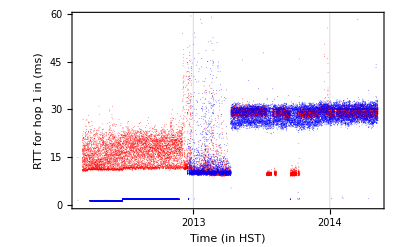
-Graphics-p1178p1165

```mathematica
Clear[rttDateListPlot];
rttDateListPlot[dataSet_List,hop_Integer]:=
Block[{dataToUse, probes={1178,1165},pointSize},
dataToUse=Cases[tMeasurements,
{"probe_id"->probeID_/; probeID==#,
"measurement_id"->measurementID_/; measurementID==hop,
"resolution"->resolution_,
"received"->received_,
"rtt_5pct"-> rtt5pct_,
"rtt_95pct"->rtt95pct_,
"rtt_med"->rttMed_,
"sent"->sent_,
"timestamp"->timestamp_}->{timestamp,rttMed}]&/@probes;
pointSize=1/(1000); 
Labeled[
DateListPlot[
dataToUse, 
PlotStyle->{{Red,PointSize[pointSize]},{Blue,PointSize[pointSize]}},
FrameLabel->{{"RTT for hop "<>ToString[hop]<>" in (ms)",None},{"Time (in HST)",None}}],
{
Style["p1178",Red,Bold,"Section"], 
Style["p1165",Blue,Bold,"Section"]},
{Top,Bottom}]];
rttDateListPlot[tMeasurements,1]
```

```mathematica
selectElements[list_,start_,end_]:=Module[{s=AbsoluteTime@start,e=AbsoluteTime@end},Select[list,Composition[s≤#≤e&,AbsoluteTime,First]]]
```

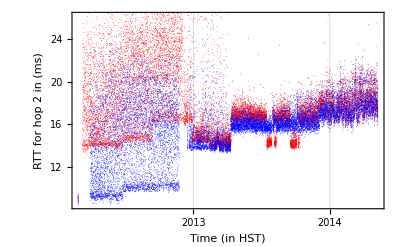
-Graphics-p1178p1165

```mathematica
rttDateListPlot[tMeasurements,2]
```

```mathematica
Clear[rttMedBand];
rttMedBand[dataSet_List, probes_List,hop_Integer, interval_Interval, inInterval_]:=
Cases[dataSet,
{"probe_id"->probeID_/; probeID==#,
"measurement_id"->measurementID_/; measurementID==hop,
"resolution"->resolution_,
"received"->received_,
"rtt_5pct"-> rtt5pct_,
"rtt_95pct"->rtt95pct_,
"rtt_med"->rttMed_/; If[inInterval, IntervalMemberQ[interval ,rttMed], Not[IntervalMemberQ[interval ,rttMed]]] ,
"sent"->sent_,
"timestamp"->timestamp_}->{timestamp,rttMed}]&/@probes;
(* TEST *)
rttMedBand[tMeasurements,{10546},1,Interval[{5.0,23.5}], True]//TableForm
```

2013 | 12 | 24 | 21 | 0 | 0.
21.997 |  |  |  |  |

```mathematica
uncongested=rttMedBand[tMeasurements,{1165,1178},1,Interval[{5.0,10.0}], True];
congested=rttMedBand[tMeasurements,{1165,1178},1,Interval[{5.0,10.0}], False];
{Dimensions[uncongested],Dimensions[congested]}//TableForm
```

2
2

```mathematica
rttDateListPlotWrapper[dataToUse_List,probes_List, hop_Integer, title_String]:=
Block[{pointSize},
pointSize=1/(1000); 
Labeled[
DateListPlot[
dataToUse, 
PlotStyle->{{Red,PointSize[pointSize]},{Blue,PointSize[pointSize]}},
PlotRange->{{{2012,1,1,0,0}, DateList[]},{0.0, 70}},
FrameLabel->{{"RTT for hop "<>ToString[hop]<>" in (ms)",None},{"Time (in HST)",None}}],
{
Style["p1178",Red,Bold,"Section"], 
Style["p1165",Blue,Bold,"Section"]},
{Top,Bottom}]];
```

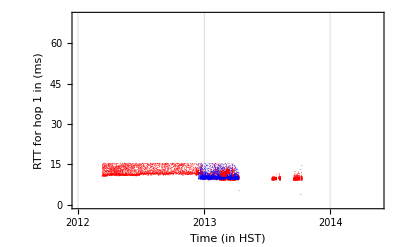
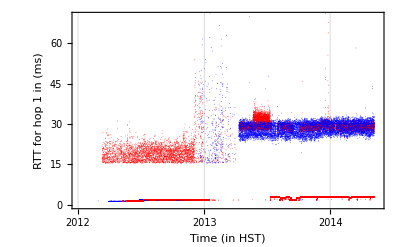
{{-Graphics-p1178p1165,-Graphics-p1178p1165},{9358,41817},{18.2863%,81.7137%}}

```mathematica
Block[{probes={1178,1165, 2289},intervalToUse=Interval[{3.5,15.5}],hop=1, 
congested, uncongested, congestedTotal,uncongestedTotal},
uncongested=rttMedBand[tMeasurements,probes,hop,intervalToUse, True];
congested=rttMedBand[tMeasurements,probes,hop,intervalToUse, False];
uncongestedTotal=Total[Length[#]&/@uncongested];
congestedTotal=Total[Length[#]&/@congested];
{{rttDateListPlotWrapper[uncongested,probes,hop,"UNCONGESTED"],
rttDateListPlotWrapper[congested,probes,hop,"CONGESTED"]},
{uncongestedTotal,congestedTotal},
{ToString[100N[uncongestedTotal/(uncongestedTotal + congestedTotal)]]<> "%",ToString[100N[congestedTotal/(uncongestedTotal + congestedTotal)]]<>"%"}}
]
```

```mathematica
(* scratch -- convert to the DateListPlotWrapper *)
```

```mathematica
Clear[rttDateListPlot];
rttDateListPlot[dataSet_List,hop_Integer]:=
Block[{dataToUse, probes={1178,1165},pointSize},
dataToUse=Cases[tMeasurements,
{"probe_id"->probeID_/; probeID==#,
"measurement_id"->measurementID_/; measurementID==hop,
"resolution"->resolution_,
"received"->received_,
"rtt_5pct"-> rtt5pct_,
"rtt_95pct"->rtt95pct_,
"rtt_med"->rttMed_,
"sent"->sent_,
"timestamp"->timestamp_}->{timestamp,rttMed}]&/@probes;
pointSize=1/(1000); 
Labeled[
DateListPlot[
dataToUse, 
PlotStyle->{{Red,PointSize[pointSize]},{Blue,PointSize[pointSize]}},
FrameLabel->{{"RTT for hop "<>ToString[hop]<>" in (ms)",None},{"Time (in HST)",None}}],
{
Style["p1178",Red,Bold,"Section"], 
Style["p1165",Blue,Bold,"Section"]},
{Top,Bottom}]];
rttDateListPlot[tMeasurements,1]
```

-Graphics-p1178p1165

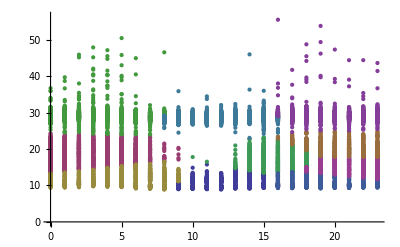

```mathematica
Clear[rttHourOfDay];
rttHourOfDay[tData_List,probes_, hop_Integer,measurement_String]:=
Block[{slice,slicesThatMatched,rttByHour},
slice={"timestamp",measurement,"probe_id","measurement_id"}/.tData;
slicesThatMatched=Cases[slice,{timestamp_,measure_,probes,hop}->{timestamp,measure}];
rttByHour={#[[1]][[4]],#[[2]]}&/@slicesThatMatched;

rttByHour]
(* TEST *)
ListPlot[FindClusters[rttHourOfDay[tMeasurements,1178,1,"rtt_med"],12]]
```